```mathematica
Clear["Global`*"]
M = 40;
kb=1.381*10^(-5); T = 1 *10^5;
J=1;
σ = Table[Table[2RandomInteger[]-1,{i,1,M}],{j,1,M}];
 k = J/(kb T);
k = 0.6;
  list= {Exp[-4 k],Exp[-8k]}//N;
(*list2 = {MatrixPlot[σ,ColorFunction->"BlueGreenYellow",Mesh->All,FrameTicks->All]};*)
list2={};
p[kp_] := p[kp] = If[kp==4,list[[1]],list[[2]]];
f[spins_,i_,j_] :=f[spins,i,j]=(
var1 = i -1; var3 = j-1; var2 = i+1; var4 = j+1;
 If[var1 == 0, var1=M,If[var1 ==M-1, var2 = 1]];
 If[var3 == 0, var3=M,If[var3 ==M-1, var4 = 1]];
spins[[i,j]]*(spins[[var1,j]]+spins[[var2,j]]+spins[[i,var3]]+spins[[i,var4]]));
U = -(J/2)( Sum[Sum[f[σ,i,j],{i,1,M}],{j,1,M}]);
energy[0] = U;
(*energy[m_] := energy[m-1] + ΔU;*)
```

```mathematica
m=1;
Do[
iv =RandomInteger[{1,M}]; jv = RandomInteger[{1,M}];
ΔU =2 J f[σ,iv,jv];
σ[[iv,jv]] = -σ[[iv,jv]];
If[ΔU > 0 ,If[RandomReal[] >p[ΔU],
σ[[iv,jv]] = -σ[[iv,jv]];
ΔU = 0;
];
];
energy[m] = energy[m-1]+ΔU;
If[Mod[m,500] == 0,list2=Append[list2,ArrayPlot[σ,ColorFunction->"BlueGreenYellow",Mesh->All,FrameTicks->All,PlotRangePadding->0,Background->None]]];
,{m,1,25000}]
```

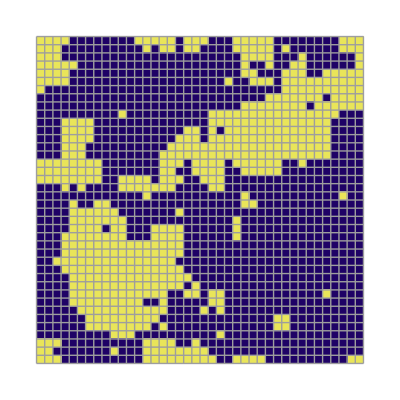

```mathematica
ArrayPlot[σ,ColorFunction->"BlueGreenYellow",Mesh->All,FrameTicks->All,PlotRangePadding->0]
```

```mathematica
anim=ListAnimate[list2]
```

```mathematica
Export["ising.gif",list2]
```

ising.gif

```mathematica
Length[list2]
```

201

```mathematica
energy[0]
energy[200000]
```

68

-2784

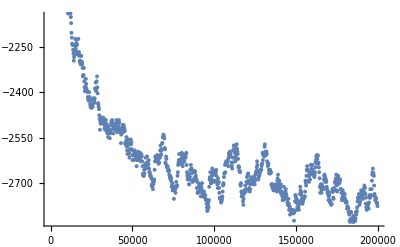

```mathematica
ListPlot[Table[{m,energy[m]},{m,1,200000,200}]]
```